## Source is https://www.thelancet.com/article/S0140-6736(20)32318-7/fulltext

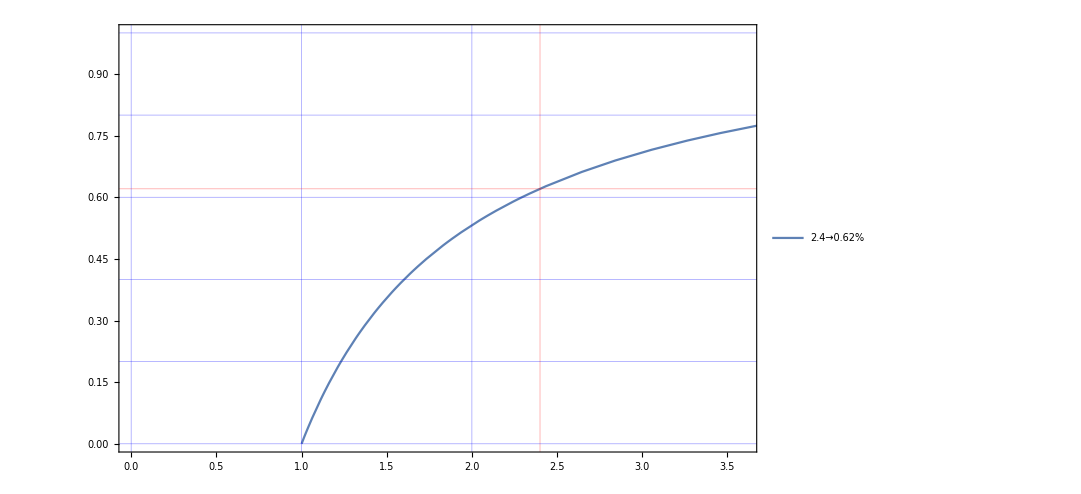

```mathematica
Block[{efficiency=0.94, Rzero=2.4},
f[R_]:=(1-1/R)/efficiency;
Plot[f[R],{R,0,10},GridLines->{Join[Table[{x,Blue},{x,0,2}],{{Rzero,Directive[Thick, Red]}}], Join[Table[{x,Blue},{x,0,1,0.2}],{{f[Rzero],Directive[Thick, Red]}}]},  PlotRange->{{0,3/2*Rzero},{0,1}}, PlotLegends->{Rzero->ToString[Round[f[Rzero],0.01],InputForm]<> "%"}, ImageSize->800, Frame->True]
]
```

```mathematica
1-1/R//Factor
```

(-1+R)/R

```mathematica
Join[Table[{x},{x,0,2}],{{Rzero,Directive[Thick, Red]}}]
```

{{0},{1},{2},{Rzero,Directive[Thickness[Large],RGBColor[1, 0, 0]]}}

```mathematica
Join[Table[x->Blue,{x,0,2}],{Rzero->Directive[Thick, Red]}]
```

{0→RGBColor[0, 0, 1],1→RGBColor[0, 0, 1],2→RGBColor[0, 0, 1],Rzero→Directive[Thickness[Large],RGBColor[1, 0, 0]]}